```mathematica
f[q_]:=1/Pi*If[q>2,0,If[q>1,1/4*(2-q)^3,1/4*(2-q)^3-(1-q)^3]]
W[r_,h_]=1/h^3 *f[r/h]
```

If[r/h>2,0,If[r/h>1,1/4 (2-r/h)^3,1/4 (2-r/h)^3-(1-r/h)^3]]/(h^3 π)

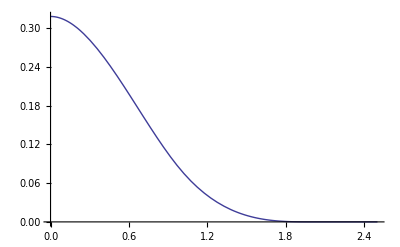

```mathematica
Plot[W[r,1],{r,0,2.5}]
```

```mathematica
N[Expand[(1/4*(2-q)^3-(1-q)^3)/Pi]]
```

0.31831-0.477465 q^2+0.238732 q^3

```mathematica
N[Expand[(1/4*(2-q)^3)/Pi]]
```

0.63662-0.95493 q+0.477465 q^2-0.0795775 q^3

```mathematica
DWr[r_,h_]:=Derivative[1,0][W][r,h]
DWh[r_,h_]:=Derivative[0,1][W][r,h]
```

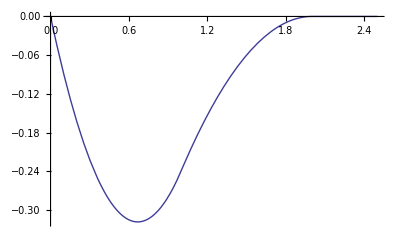

```mathematica
Plot[DWr[r,1],{r,0,2.5}]
```

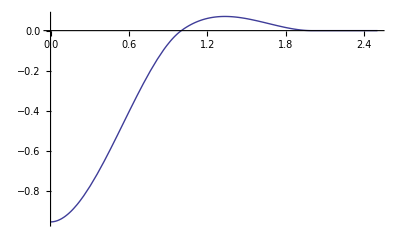

```mathematica
Plot[DWh[r,1],{r,0,2.5},PlotRange->Full]
```

```mathematica
DWr[r,h]
```

If[r/h>2,0,If[r/h>1,-(3 (2-r/h)^2)/(4 h),(3 (1-r/h)^2)/h-(3 (2-r/h)^2)/(4 h)]]/(h^3 π)

```mathematica
N[Expand[3/4 (2-q)^2/Pi]]
```

0.95493-0.95493 q+0.238732 q^2

```mathematica
N[Expand[(3 (1-q)^2-3/4 (2-q)^2)/Pi]]
```

-0.95493 q+0.716197 q^2

```mathematica
DWh[r,h]
```

If[r/h>2,0,If[r/h>1,(3 r (2-r/h)^2)/(4 h^2),-(3 r (1-r/h)^2)/h^2+(3 r (2-r/h)^2)/(4 h^2)]]/(h^3 π)-(3 If[r/h>2,0,If[r/h>1,1/4 (2-r/h)^3,1/4 (2-r/h)^3-(1-r/h)^3]])/(h^4 π)